## Spatially explicit producer-sensitive-degrader interactions

```mathematica
g = 0.7;
cp = 0.1;
cd=0.05;
dee = 0.2;
up = 10;
ud = 10;
σ = 3;
δP=50;
δD =10;
timeperiod = 10;
```

```mathematica
cstar = (Log[0.1/(1-dee)])/(Log[0.01/(1-dee)]);
τ = up (cstar G[1,σ] - G[σ, σ])/(cstar-1);
k = ((cstar-1) Log[0.1/(1-dee)])/(up*(G[1,σ]-G[σ,σ]));
```

```mathematica
fP = g - cp-dee;
fD = g-cd-dee;
```

```mathematica
Pd[c_] := If[c<τ,dee ,dee+(1-dee)(1-Exp[k(τ-c)])];
G[dist_, dev_]:= Exp[(-dist^2)/(2 dev^2)]/(2 π dev);
```

```mathematica
eqs={D[p[t,x,y],t] == p[t,x,y]*(fP - (p[t,x,y]fP + s[t,x,y](g - Pd[Ab[t,x,y]-Dg[t,x,y]])+d[t,x,y]fD)),
D[s[t,x,y],t] == s[t,x,y]*((g - Pd[Ab[t,x,y]-Dg[t,x,y]]) - (p[t,x,y]*fP + s[t,x,y](g - Pd[Ab[t,x,y]-Dg[t,x,y]])+d[t,x,y]*fD)),
D[d[t,x,y],t] == d[t,x,y]*(fD - (p[t,x,y]*fP + s[t,x,y] (g - Pd[Ab[t,x,y]-Dg[t,x,y]])+d[t,x,y]*fD)),
D[Ab[t,x,y],t] == δP(D[Ab[t,x,y],{x,2}]+D[Ab[t,x,y],{y,2}]) + up p[t,x,y]-Ab[t,x,y] Dg[t,x,y],
D[Dg[t,x,y],t] == δD(D[Dg[t,x,y],{x,2}]+D[Dg[t,x,y],{y,2}]) + ud d[t,x,y]-Ab[t,x,y] Dg[t,x,y]
};
```

```mathematica
inits={Ab[0,x,y]==0,
Dg[0,x,y]==0,
p[0,x,y]==Sin[x+y],
s[0,x,y]== 1-(x-0.5)^2 - (y-0.5)^2,
d[0,x,y]==Cos[x+y]};
```

```mathematica
bc={PeriodicBoundaryCondition[Ab[t,x,y],x==0,TranslationTransform[{1,0}]],
PeriodicBoundaryCondition[Ab[t,x,y],y==0,TranslationTransform[{0,1}]],
PeriodicBoundaryCondition[Dg[t,x,y],x==0,TranslationTransform[{1,0}]],
PeriodicBoundaryCondition[Dg[t,x,y],y==0,TranslationTransform[{0,1}]],
PeriodicBoundaryCondition[p[t,x,y],x==0,TranslationTransform[{1,0}]],
PeriodicBoundaryCondition[p[t,x,y],y==0,TranslationTransform[{0,1}]],
PeriodicBoundaryCondition[s[t,x,y],x==0,TranslationTransform[{1,0}]],
PeriodicBoundaryCondition[s[t,x,y],y==0,TranslationTransform[{0,1}]],
PeriodicBoundaryCondition[d[t,x,y],x==0,TranslationTransform[{1,0}]],
PeriodicBoundaryCondition[d[t,x,y],y==0,TranslationTransform[{0,1}]]};
```

```mathematica
sol=NDSolve[{eqs,inits,bc},{Ab,Dg,p,s,d},{t,0,timeperiod},{x,0,1},{y,0,1}];
```

$Aborted

```mathematica
Manipulate[Plot3D[Evaluate[{Ab[t,x,y],Dg[t,x,y],p[t,x,y],s[t,x,y],d[t,x,y]}/.sol],{x,0,1},{y,0,1}, PlotRange->All,PlotLegends->{"Ab","Dg","P","S","D"}],{t,0,timeperiod}]
```

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
initdatap=Table[Evaluate[Flatten[p[t,x,y]/. sol[[1,3]]]//Flatten],{t,0,timeperiod,1},{y,0,1,.1},{x,0,1,.1}];
datap={};
For[i=1,i<Length[Range[0,timeperiod,1]]+1,i++,AppendTo[datap,Total[Flatten[initdatap[[i]]]]]]
initdatas=Table[Evaluate[Flatten[s[t,x,y]/. sol[[1,4]]]//Flatten],{t,0,timeperiod,1},{y,0,1,.1},{x,0,1,.1}];
datas={};
For[i=1,i<Length[Range[0,timeperiod,1]]+1,i++,AppendTo[datas,Total[Flatten[initdatas[[i]]]]]]
initdatad=Table[Evaluate[Flatten[d[t,x,y]/. sol[[1,5]]]//Flatten],{t,0,timeperiod,1},{y,0,1,.1},{x,0,1,.1}];
datad={};
For[i=1,i<Length[Range[0,timeperiod,1]]+1,i++,AppendTo[datad,Total[Flatten[initdatad[[i]]]]]];
datap=datap/(datap+datas+datad);
datas=datas/(datap+datas+datad);
datad=datad/(datap+datas+datad);
```

```mathematica
colors={{0.172549,0.482353,0.713725},{0.843137,0.29,0.29},{0.670588,0.85098,1},{0.992157,0.682353,0.380392}};
```

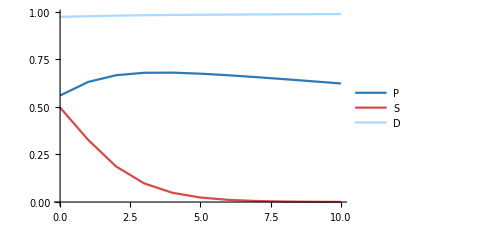

```mathematica
ListPlot[{Transpose[{Range[0,timeperiod,1],datap}],Transpose[{Range[0,timeperiod,1],datas}],Transpose[{Range[0,timeperiod,1],datad}]},Joined->True,PlotLegends->{"P","S","D"},
PlotStyle->{RGBColor[colors[[1]]],RGBColor[colors[[2]]],RGBColor[colors[[3]]]}]
```